```mathematica
Quit[]
```

```mathematica
$Assumptions={f>0,V0>0,t>0,x0>0};
```

### H = 0

```mathematica
V[x_]=Tanh[x]^2;
```

```mathematica
dT=π/Sqrt[2(1-Tanh[x0]^2)]//Simplify
xsol[t_]=ArcSinh[Cos[(π t)/dT]/Sqrt[1/Tanh[x0]^2-1]]//Simplify
```

(π Cosh[x0])/(√2)

ArcSinh[Cos[√2 t Sech[x0]] Sinh[x0]]

```mathematica
xsol[0]//Simplify
xsol[dT]//Simplify
xsol'[0]
```

x0

-x0

0

```mathematica
Simplify[xsol''[t]+V'[xsol[t]]]
```

0

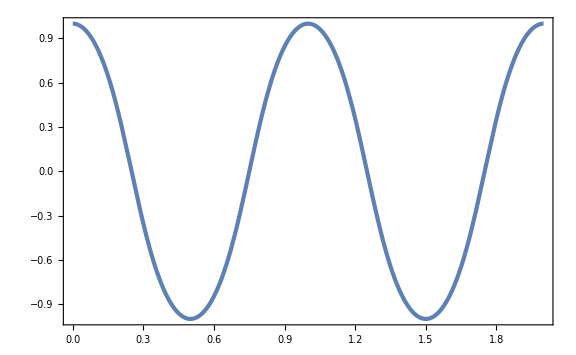

```mathematica
Plot[xsol[tp 2dT]/.{x0->1},{tp,0,2}]
```

```mathematica
V''[x]//Simplify
```

-2 (-2+Cosh[2 x]) Sech[x]^4

```mathematica
Vpp[t_]=V''[xsol[t]]//Simplify;
```

```mathematica
dT
```

(π Cosh[x0])/(√2)

```mathematica
VppMean=1/dT Integrate[Vpp[t],{t,0,dT}]
```

Sech[x0] (-1+3 Sech[x0]^2)

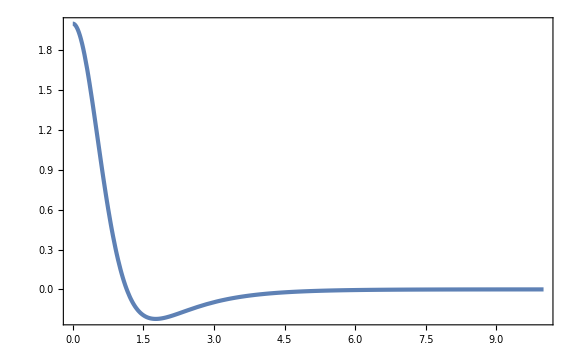

```mathematica
Plot[VppMean,{x0,0,10},PlotRange->Full]
```

```mathematica
Integrate[(Vpp[t]-VppMean),{t,0,dT}]
```

0

```mathematica
VppVar=1/dT Integrate[Vpp[t]^2,{t,0,dT}]-VppMean^2//Simplify
```

1/8 (447+468 Cosh[x0]+92 Cosh[2 x0]+12 Cosh[3 x0]+5 Cosh[4 x0]) Sech[x0]^7 Sinh[x0/2]^4

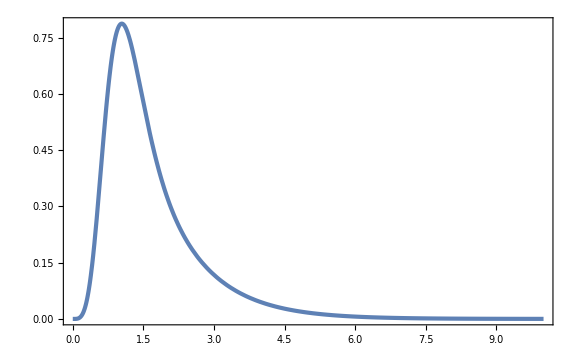

```mathematica
Plot[VppVar,{x0,0,10}]
```

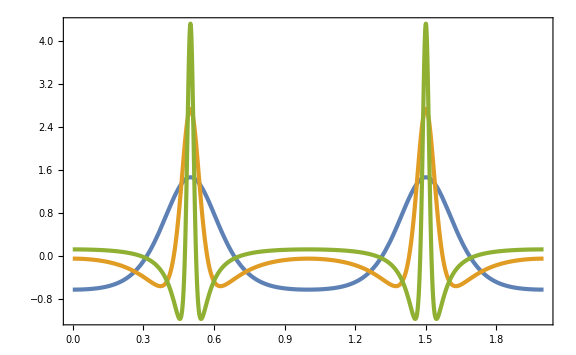

```mathematica
Plot[{(Vpp[tp dT]-VppMean)/Sqrt[2VppVar]/.{x0->1},(Vpp[tp dT]-VppMean)/Sqrt[2VppVar]/.{x0->2},(Vpp[tp dT]-VppMean)/Sqrt[2VppVar]/.{x0->3}},{tp,0,2},PlotRange->Full]
```

```mathematica
D[D[(v0 Tanh[x/x0]^2), x], x]/.{x->0}
```

(2 v0)/x0^2

```mathematica
f=10^-3;
h=0.674;
Ωm=0.3;
ρm0=3 h^2 Ωm;
V0=1.1 3(1-Ωm)h^2;
xi=7.35f;
zi=1000;
mth=Sqrt[V0]/f
m2=V''[0]
```

1024.39

2.09876×10^6

```mathematica
V[x_]=V0 Tanh[x/f]^2;
H[x_,p_,z_]=Sqrt[(p^2/2+V[x]+ρm0(1+z)^3)/3];
```

```mathematica
Hi=H[xi,0,zi];
tf=20000/Hi;
tVppmax={};
```

```mathematica
bgsol=NDSolve[{x''[t]+3H[x[t],x'[t],z[t]]x'[t]+V'[x[t]]==0,z'[t]==-(1+z[t])H[x[t],x'[t],z[t]],x[0]==xi,x'[0]==0,z[0]==zi,WhenEvent[V'''[x[t]]==0&&V''[x[t]]>0,AppendTo[tVppmax,t]],WhenEvent[z[t]==0,t0=t]},{x[t],x'[t],z[t]},{t,0,tf}(*,WorkingPrecision->50,MaxSteps->1000000*)][[1]];
```

```mathematica
xsol[t_]=x[t]/.bgsol;
psol[t_]=x'[t]/.bgsol;
zsol[t_]=z[t]/.bgsol;
Hsol[t_]=H[xsol[t],psol[t],zsol[t]];
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
Vppsol[t_]=V''[xsol[t]];
```

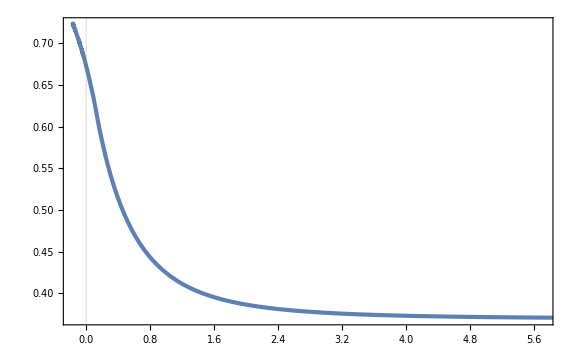

```mathematica
ParametricPlot[{zsol[t],(1+zsol[t])^(-3/2)Hsol[t]},{t,0,tf},GridLines->{{0},None}]
```

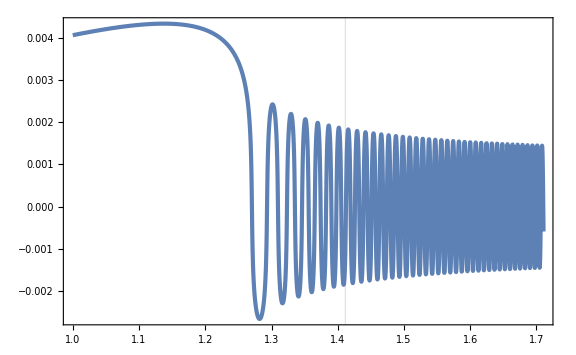

```mathematica
Plot[(1+zsol[t])^(-3/2)xsol[t],{t,1,tf},PlotRange->Full,GridLines->{{t0},None}]
```

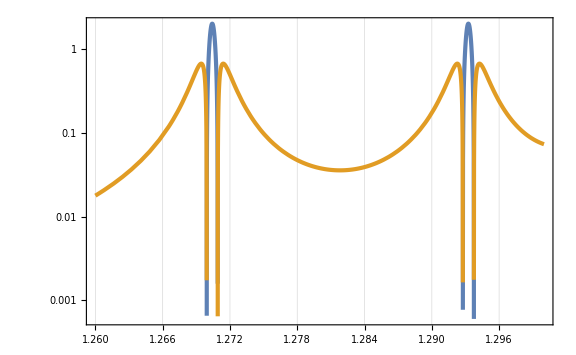

```mathematica
LogPlot[{Vppsol[t]/mth^2,-Vppsol[t]/mth^2},{t,1.26,1.3},GridLines->{tVppmax,None}]
```

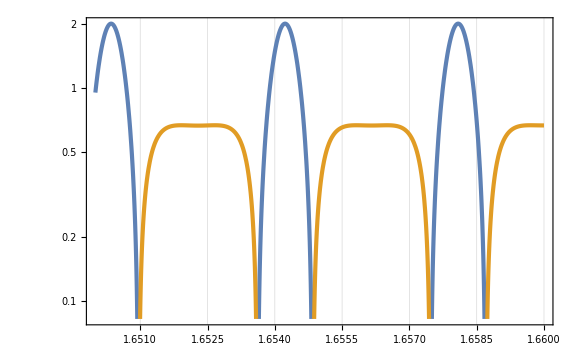

```mathematica
LogPlot[{Vppsol[t]/mth^2,-Vppsol[t]/mth^2},{t,1.65,1.66},GridLines->{tVppmax,None}]
```

```mathematica
TList=Table[mth(tVppmax[[i+1]]-tVppmax[[i]]),{i,Length[tVppmax]-1}]
```

{23.3954,16.8741,13.9723,12.2407,11.0589,10.1871,9.51008,8.96482,8.51363,8.13236,7.80472,7.51929,7.26774,7.04394,6.84314,6.6617,6.49672,6.34587,6.20727,6.07937,5.96085,5.85066,5.74786,5.65168,5.56144,5.47657,5.39656,5.32097,5.24942,5.18156,5.1171,5.05576,4.9973,4.94151,4.88819,4.83719,4.78832,4.74145,4.69645,4.65321,4.61161,4.57156,4.53296,4.49573,4.4598,4.42508,4.39153,4.35906,4.32764,4.2972,4.2677,4.23909,4.21132,4.18437,4.15819,4.13274,4.10799,4.08392,4.06049,4.03768,4.01546,3.99381,3.97269,3.9521,3.93201,3.91241,3.89327,3.87457,3.85631,3.83846,3.821,3.80394,3.78725,3.77091,3.75493,3.73928,3.72395,3.70894}

```mathematica
VppMeanList=Table[1/(tVppmax[[i+1]]-tVppmax[[i]])NIntegrate[Vppsol[t],{t,tVppmax[[i]],tVppmax[[i+1]]}],{i,Length[tVppmax]-1}];//AbsoluteTiming
```

{11.147,Null}

```mathematica
qList=Table[1/(tVppmax[[i+1]]-tVppmax[[i]])NIntegrate[(Vppsol[t]-VppMeanList[[i]])^2/(2 m2^2),{t,tVppmax[[i]],tVppmax[[i+1]]}],{i,Length[tVppmax]-1}];//AbsoluteTiming
```

{13.2172,Null}

```mathematica
qList
```

{0.0140528,0.0193526,0.0233856,0.0267996,0.0298346,0.0326074,0.0351844,0.0376071,0.0399026,0.0420899,0.0441829,0.0461918,0.0481247,0.0499877,0.0517861,0.0535239,0.0552045,0.056831,0.0584059,0.0599313,0.0614094,0.0628418,0.0642302,0.065576,0.0668807,0.0681455,0.0693715,0.0705598,0.0717114,0.0728276,0.0739091,0.0749568,0.0759716,0.0769544,0.077906,0.078827,0.0797184,0.0805809,0.0814151,0.0822216,0.0830011,0.0837544,0.084482,0.0851846,0.0858627,0.0865169,0.0871479,0.087756,0.0883419,0.0889062,0.0894492,0.0899715,0.0904737,0.0909561,0.0914192,0.0918636,0.0922895,0.0926975,0.093088,0.0934614,0.0938181,0.0941585,0.0944829,0.0947919,0.0950856,0.0953646,0.095629,0.0958793,0.0961158,0.0963389,0.0965488,0.0967459,0.0969305,0.0971028,0.0972632,0.097412,0.0975494,0.0976757}

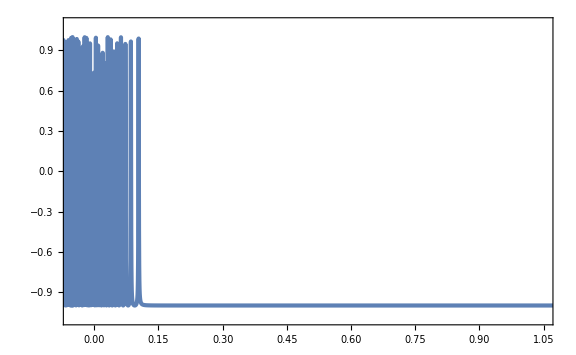

```mathematica
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotRange->{{-0.05,1.05},{-1.1,1.1}}]
```